```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/beams/nmmToL0AFEND_2bunch_2024-02-16Clean/2024-02-16_2bunch_1e5Downsample_nudgeWeights.h5","Data"];
Keys[raw]
```

{/id,/momentum/x,/momentum/y,/momentum/z,/position/x,/position/y,/position/z,/time,/weight}

```mathematica
keys = {"id","px","py","pz","x","y","z","t","weight"};
```

```mathematica
data=Table[
AssociationThread[keys,Values[raw[[All,i]]]],
{i,Length[raw["/id"]]}
];
```

```mathematica
{witnessWeight, driverWeight} = Sort[DeleteDuplicates[raw[["/weight"]]]]
```

{2.09611×10^-14,2.10031×10^-14}

```mathematica
driverData = Select[data,#weight == driverWeight&];
witnessData = Select[data,#weight == witnessWeight&];
```

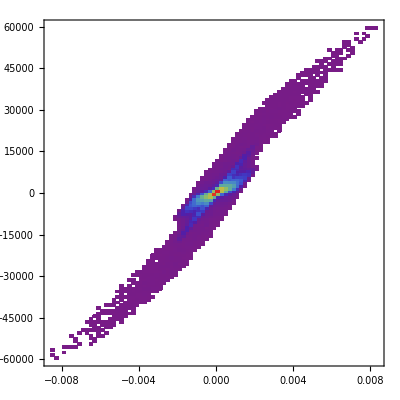

```mathematica
DensityHistogram[{#x,#px}&/@driverData,{100,100},ColorFunction->"Rainbow"]
```

```mathematica
ListPointPlot3D[{#x,#px,#t}&/@driverData,SphericalRegion->True,ImageSize->800,ColorFunction->"Rainbow",BoxRatios->{1,1,1}]
```

-Graphics3D-

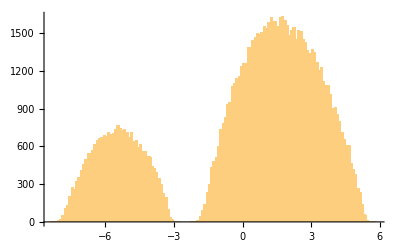

```mathematica
Histogram[#t&/@data,100]
```